# Math 223: Homework 7

Ali Heydari

March. 18th, 2021

## Problem 1

Find the first two terms of the asymptotic expansion of:

For this Laplace integral (which is of the form ), we can perform IBP to obtain the asymptotic expansion. Doing IBP, will get:
 = 

Now if we continue with IBP, then the next term will be . So we will show that  is smaller than the first two terms, so that we can get an asymptotic relation that approximates  well.

```mathematica
numerator = (1/x) *  Integrate[E^(-x*t)/t^2,{t,5,9},Assumptions->x>0]
```

((1/45 ⅇ^(-9 x) (-5+9 ⅇ^(4 x))-x ExpIntegralEi[-9 x]+x ExpIntegralEi[-5 x]) (Assumptions→x>0))/x

```mathematica
denom = -E^(-9x)/(9x) +E^(-5x)/(5x)
```

-ⅇ^(-9 x)/(9 x)+ⅇ^(-5 x)/(5 x)

```mathematica
Limit[numerator/denom, x-> ∞]
```

0

this result solidifies that the remainder terms in the asymptotic expansion will be smaller than the first two terms we recovered. So now we can see how well our approximations have been using a LogPlot:

```mathematica
exactSol=Integrate[E^(-x*t)/t,{t,5,9}]
```

ExpIntegralEi[-9 x]-ExpIntegralEi[-5 x]

```mathematica
approx = denom
```

-ⅇ^(-9 x)/(9 x)+ⅇ^(-5 x)/(5 x)

Now plotting the semi-log plot and the error plot

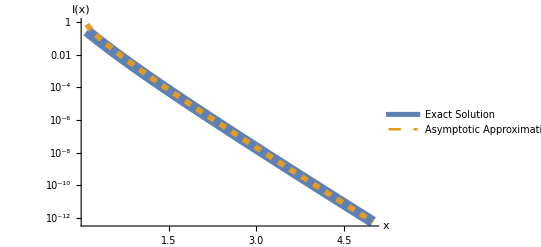

```mathematica
LogPlot[{exactSol,approx},{x,0.1,5},PlotStyle->{Directive[Solid,Thickness[0.02]],Directive[Dashed,Thickness[0.01]]}, AxesLabel->{Style["x",Italic,18],Style["I(x)", Italic, 18]}, TicksStyle->Directive[FontSize->14],PlotLegends->{"Exact Solution", "Asymptotic Approximation"}]
```

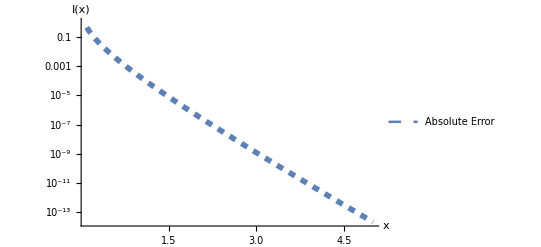

```mathematica
absErr = Abs[exactSol - approx];
LogPlot[absErr ,{x,0.1,5},PlotStyle->{Directive[Solid,Thickness[0.02]],Directive[Dashed,Thickness[0.01]]}, AxesLabel->{Style["x",Italic,18],Style["I(x)", Italic, 18]}, TicksStyle->Directive[FontSize->14],PlotLegends->{"Absolute Error"}]
```

these plots show that for x being close to 0, our approximation is not so well, but if we move slightly pass 1, our error becomes very small! (this is very impressive, since we approximated the leading behavior as x → ∞!!)

## Problem 2

Use Watson’s lemma to determine the asymptotic expansion of:

## Problem 3

Use Laplace’s method to determine the leading behavior of: